```mathematica
Quit
```

```mathematica
sol= DSolve[{m*x''[t]==-m*g, x[0]==x0,x'[0]==v0},x[t],t];
x[t] = sol[[1]][[1]][[2]]
```

1/2 (-g t^2+2 t v0+2 x0)

```mathematica
x'[t] = D[x[t],t]
```

1/2 (-2 g t+2 v0)

```mathematica
x''[t]=D[x'[t],t]
```

-g

```mathematica
m = 3;
g= 9.8;
x0 = 0;
v0 = 10;
x[t]
```

1/2 (20 t-9.8 t^2)

Had  to  copy  and  paste  value  of  x[t]  into  plot; discussed  in  office  hours  4/24/24

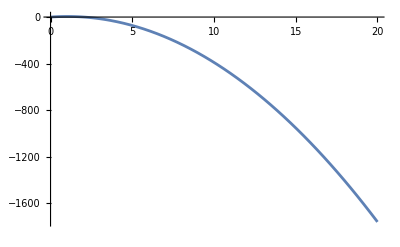

```mathematica
Plot[1/2 (20 t-9.8 t^2),{t,0,20}]
```

```mathematica
Clear[m,g,x0,v0]
```

```mathematica
soldrag = DSolve[{m*x''[td]==-m*g-b*x'[td], x[0]==x00,x'[0]==V},x[td],td];
x[td] = soldrag[[1]][[1]][[2]]
```

(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/b^2

```mathematica
x'[td] = D[x[td],td]
```

-(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/(b m)+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/b^2

```mathematica
x''[td] = D[x'[td],td]
```

```mathematica
(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/m^2+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g-(b^3 ⅇ^((b td)/m) g td)/m+(b^3 ⅇ^((b td)/m) V)/m+(b^4 ⅇ^((b td)/m) x00)/m^2))/b^2-(2 ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/(b m)
```

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
Manipulate[Plot[-(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g-(b^3 ⅇ^((b td)/m) g td)/m+(b^3 ⅇ^((b td)/m) V)/m+(b^4 ⅇ^((b td)/m) x00)/m^2))/b^2,{td,0,120}],{{m,1},-3,3},{{V,1},-10,20},{{b,0.1},0,1}]
```

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
x[td]
x'[td]
x''[td]
```

100. ⅇ^(-0.1 td) (-10.8+10.8 ⅇ^(0.1 td)-0.98 ⅇ^(0.1 td) td)

-10. ⅇ^(-0.1 td) (-10.8+10.8 ⅇ^(0.1 td)-0.98 ⅇ^(0.1 td) td)+100. ⅇ^(-0.1 td) (0.+0.1 ⅇ^(0.1 td)-0.098 ⅇ^(0.1 td) td)

ⅇ^(-0.1 td) (-10.8+10.8 ⅇ^(0.1 td)-0.98 ⅇ^(0.1 td) td)-20. ⅇ^(-0.1 td) (0.+0.1 ⅇ^(0.1 td)-0.098 ⅇ^(0.1 td) td)+100. ⅇ^(-0.1 td) (0.-0.088 ⅇ^(0.1 td)-0.0098 ⅇ^(0.1 td) td)

Position  Graph, had to insert output into plot :

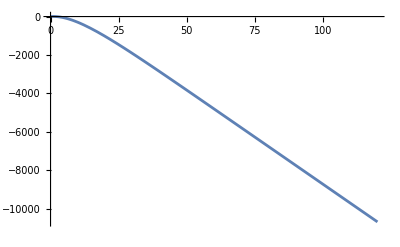

```mathematica
Plot[99.99999999999999 ⅇ^(-0.1 td) (-10.8+10.8 ⅇ^(0.1 td)-0.9800000000000001 ⅇ^(0.1 td) td),{td,0,120}]
```

Velocity  Graph, had to insert output into plot :

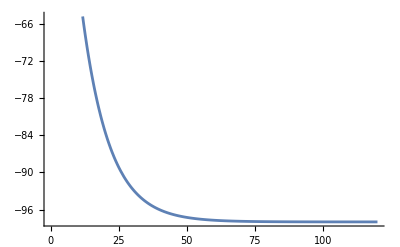

```mathematica
Plot[-10. ⅇ^(-0.1 td) (-10.8+10.8 ⅇ^(0.1 td)-0.9800000000000001 ⅇ^(0.1 td) td)+99.99999999999999 ⅇ^(-0.1 td) (0.+0.10000000000000002 ⅇ^(0.1 td)-0.09800000000000003 ⅇ^(0.1 td) td),{td,0,120}]
```

```mathematica
Manipulate[Plot[-10. ⅇ^(-0.1 td) (-10.8+10.8 ⅇ^(0.1 td)-0.9800000000000001 ⅇ^(0.1 td) td)+99.99999999999999 ⅇ^(-0.1 td) (0.+0.10000000000000002 ⅇ^(0.1 td)-0.09800000000000003 ⅇ^(0.1 td) td),{td,0,120}],{{m,1},-3,3},{{V,1},-10,20},{{b,0.1},0,1}]
```

Acceleration  graph, had to insert output into plot :

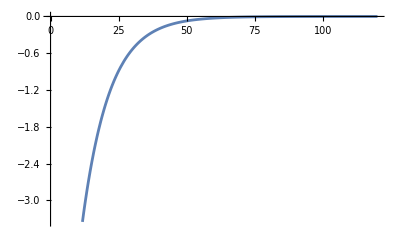

```mathematica
Plot[ⅇ^(-0.1 td) (-10.8+10.8 ⅇ^(0.1 td)-0.9800000000000001 ⅇ^(0.1 td) td)-20. ⅇ^(-0.1 td) (0.+0.10000000000000002 ⅇ^(0.1 td)-0.09800000000000003 ⅇ^(0.1 td) td)+99.99999999999999 ⅇ^(-0.1 td) (0.-0.08800000000000002 ⅇ^(0.1 td)-0.009800000000000003 ⅇ^(0.1 td) td), {td,0,120}]
```

```mathematica
Clear[m,g,x00,V,b]
```